## Poisson-equation approach, Series treatment -- (0, 2Pi) integration, all periodic BC

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
Qx0=0;
```

```mathematica
(*Clear[H0,H0c,H0s,I0cch,I0csh,I0sch,I0ssh,A0c,dA0c]*)
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
pv10[bJx_,bmux_,theta1_,theta2_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]

(*H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
A1[0,j_,theta1_]:=Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]*)
```

```mathematica
Flatten[Table[{n,j,H0[0,j,t1_]:=Release[H0[0,j,t1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0c[n,j,t1_]:=Release[H0c[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0s[n,j,t1_]:=Release[H0s[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0cch[n,j,t1_]:=Release[I0cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0sch[n,j,t1_]:=Release[I0sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0csh[n,j,t1_]:=Release[I0csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0ssh[n,j,t1_]:=Release[I0ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,F0c[n,j]:=Release[F0c[n,j]]},{n,1,5},{j,0,5}]//Simplify,1];
Flatten[Table[{n,j,F0s[n,j]:=Release[F0s[n,j]]},{n,1,5},{j,0,5}]//Simplify,1];
Flatten[Table[{n,j,E0c[n,j]:=Release[E0c[n,j]]},{n,1,5},{j,0,5}]//Simplify,1];
Flatten[Table[{n,j,E0s[n,j]:=Release[E0s[n,j]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,h1[n,j]=H1[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1];//TableForm
```

Null

```mathematica
Flatten[Table[{n,j,da0[n,j]=dA0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

```mathematica
Qx0=0
```

0

```mathematica
Table[{j,A0s[1,j,theta1]},{j,0,10}]//Simplify//TableForm;
```

0 | 0
1 | 1/5 bJ bmu Cos[theta1] Sin[theta1]
2 | 1/20 bJ^2 bmu Cos[theta1] Sin[theta1]
3 | 1/40 bJ^3 bmu Cos[theta1] Sin[theta1]
4 | 1/240 bJ^4 bmu Cos[theta1] Sin[theta1]
5 | 1/960 bJ^5 bmu Cos[theta1] Sin[theta1]
6 | (bJ^6 bmu Cos[theta1] Sin[theta1])/7680
7 | (bJ^7 bmu Sin[2 theta1])/92160
8 | (bJ^8 bmu Sin[2 theta1])/921600
9 | (bJ^9 bmu Sin[2 theta1])/7372800
10 | (bJ^10 bmu Sin[2 theta1])/88473600

```mathematica
Table[{j,A0c[1,j,theta1]},{j,0,10}]//Simplify//TableForm;
```

0 | bmu
1 | 1/10 bJ (-5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1]))
2 | 1/40 bJ^2 bmu (10+Cos[2 theta1])
3 | 1/80 bJ^3 (-5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1]))
4 | 1/960 bJ^4 bmu (15+2 Cos[2 theta1])
5 | (bJ^5 (-5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/1920
6 | (bJ^6 bmu (20+3 Cos[2 theta1]))/46080
7 | (bJ^7 (-5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/92160
8 | (bJ^8 bmu (25+4 Cos[2 theta1]))/3686400
9 | (bJ^9 (-5 Qx0 Cos[theta1]+bmu (5+Cos[2 theta1])))/7372800
10 | (bJ^10 bmu (6+Cos[2 theta1]))/88473600

```mathematica
nmax=5;jmax=5;
pv10[1,1,theta1,theta2]/.{theta1->Pi/4,theta2->Pi/5}//N
pv20[1,1,theta2,theta1]/.{theta1->Pi/4,theta2->Pi/5}//N
```

-1.48618

-1.48616

```mathematica
Table[{j,A1s[1,j,theta1]},{j,0,10}]//Simplify//TableForm;
```

0 | A1s[1,0,theta1]
1 | A1s[1,1,theta1]
2 | A1s[1,2,theta1]
3 | A1s[1,3,theta1]
4 | A1s[1,4,theta1]
5 | A1s[1,5,theta1]
6 | A1s[1,6,theta1]
7 | A1s[1,7,theta1]
8 | A1s[1,8,theta1]
9 | A1s[1,9,theta1]
10 | A1s[1,10,theta1]

```mathematica
Table[{j,A0c[2,j,theta1]},{j,0,10}]//Simplify//TableForm;
```

0 | 0
1 | 1/10 bJ bmu Cos[theta1]
2 | (bJ^2 (52 bmu Cos[theta1]-65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/2080
3 | (bJ^3 bmu (39 Cos[theta1]+5 Cos[3 theta1]))/3120
4 | (bJ^4 (52 bmu Cos[theta1]-65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/24960
5 | (bJ^5 bmu (26 Cos[theta1]+5 Cos[3 theta1]))/49920
6 | (bJ^6 (52 bmu Cos[theta1]-65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/798720
7 | (bJ^7 bmu (13 Cos[theta1]+3 Cos[3 theta1]))/1198080
8 | (bJ^8 (52 bmu Cos[theta1]-65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/47923200
9 | (bJ^9 bmu (39 Cos[theta1]+10 Cos[3 theta1]))/287539200
10 | (bJ^10 (52 bmu Cos[theta1]-65 Qx0 Cos[2 theta1]+20 bmu Cos[3 theta1]))/4600627200

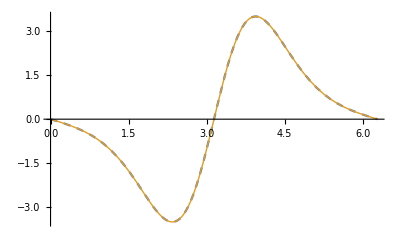

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
nmax=1;jmax=10;
(*pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify*)
```

```mathematica
(-81007533 Sin[theta1]-12402349 Sin[2 theta1-theta2])/44236800;
```

```mathematica
(-162015066 Sin[theta1]-12402349 Sin[theta1-2 theta2])/88473600;
```

-(3 Sin[theta1])/2-1/5 Sin[2 theta1-theta2]

-(3 Sin[theta1])/2-1/10 Sin[theta1-2 theta2]

π

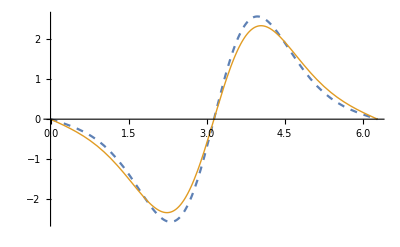

```mathematica
nmax=jmax=1;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
myt2=Pi
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

#### test

```mathematica
Qx0=0;
```

```mathematica
pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]
```

```mathematica
bmu=1;bJ=1;
A0s[1,0,theta1]//Simplify
A0s[1,1,theta1]//Simplify
A0c[1,0,theta1]//Simplify
A0c[1,1,theta1]//Simplify
```

0

1/5 Cos[theta1] Sin[theta1]

1

1/10 (5+Cos[2 theta1])

```mathematica
(A0s[1,0,theta1] +A0s[1,1,theta1] )Cos[theta2]-(A0c[1,0,theta1] +A0c[1,1,theta1] )Sin[theta2]-pv20[1,1,theta1,theta2]//Simplify
```

0

```mathematica
nmax=jmax=1;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

-(3 Sin[theta1])/2-1/5 Sin[2 theta1-theta2]

-(3 Sin[theta1])/2-1/10 Sin[theta1-2 theta2]

```mathematica
nmax=1; jmax=2;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

1/4 (-7 Sin[theta1]-Sin[2 theta1-theta2])

-(7 Sin[theta1])/4-1/8 Sin[theta1-2 theta2]

```mathematica
nmax= jmax=5;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

-(703 Sin[theta1])/384-(11 Sin[4 theta1-5 theta2])/39360-Sin[6 theta1-5 theta2]/39040-(19 Sin[3 theta1-4 theta2])/6400-(11 Sin[5 theta1-4 theta2])/31488-(121 Sin[2 theta1-3 theta2])/4992-(19 Sin[4 theta1-3 theta2])/4800-(269 Sin[theta1-2 theta2])/1920-(121 Sin[3 theta1-2 theta2])/3328-269/960 Sin[2 theta1-theta2]

-(703 Sin[theta1])/384-Sin[5 theta1-6 theta2]/46848+1/10233600(-2860 Sin[4 theta1-5 theta2]-30381 Sin[3 theta1-4 theta2]-3575 Sin[5 theta1-4 theta2]-248050 Sin[2 theta1-3 theta2]-40508 Sin[4 theta1-3 theta2]-1433770 Sin[theta1-2 theta2]-372075 Sin[3 theta1-2 theta2]-2867540 Sin[2 theta1-theta2])

```mathematica
nmax=5; jmax=10;
pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify
```

$Aborted

### import

```mathematica
(*Qx0=0*)
```

0

```mathematica
(*H0x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0x.xls"],1];*)
```

```mathematica
(*For[i=0,i<11,i++,
Print[ i,",",H0[0,i,theta1]-ToExpression[H0x[[i+1,2]]]]]*)
```

0,0

1,0

2,0

3,0

4,0

5,0

6,0

7,0

8,0

9,0

10,0

```mathematica
(*H0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0cx.xls"],1];*)
```

```mathematica
(**)
```

```mathematica
(*For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , Simplify[H0c[i,j,theta1]-ToExpression[H0cx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*H0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0sx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
test=Simplify[H0s[i,j,theta1]-ToExpression[H0sx[[11*(i-1)+j+1,3]]]] ;
If[test==0,Print["pased"],Print[i," , ", j, " , " ,test]
 ]
]
]*)
```

pased

pased

pased

«18 more identical outputs»

$Aborted

```mathematica
(*I0cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cchx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , I0cch[i,j,theta1]-ToExpression[I0cchx[[11*(i-1)+j+1,3]]] ]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*I0schx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0schx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , Simplify[I0sch[i,j,theta1]-ToExpression[I0schx[[11*(i-1)+j+1,3]]] ]]
]
]*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*I0cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cshx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , Simplify[I0csh[i,j,theta1]-ToExpression[I0cshx[[11*(i-1)+j+1,3]]] ]]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*I0sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0sshx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , Simplify[I0sch[i,j,theta1]-ToExpression[I0schx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*F0s[1,5,theta1]*)
```

F0s[1,5,theta1]

```mathematica
(*F0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0sx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<11,j++,
Print[i," , ", j, " , " , Simplify[F0s[i,j]-ToExpression[F0sx[[11*(i-1)+j+1,3]]]] ]
]
]
*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0.

1 , 3 , 0

1 , 4 , 0.

1 , 5 , 0

1 , 6 , 0

1 , 7 , 0

1 , 8 , 0

1 , 9 , 0

1 , 10 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

2 , 6 , 0

2 , 7 , 0

2 , 8 , 0

2 , 9 , 0

2 , 10 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0.

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

3 , 6 , 0

3 , 7 , 0

3 , 8 , 0

3 , 9 , 0

3 , 10 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0.

4 , 4 , 0

4 , 5 , 0

4 , 6 , 0

4 , 7 , 0

4 , 8 , 0

4 , 9 , 0

4 , 10 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0.

5 , 5 , 0

5 , 6 , 0

5 , 7 , 0

5 , 8 , 0

5 , 9 , 0

5 , 10 , 0

```mathematica
(*F0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0cx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[F0c[i,j]-ToExpression[F0cx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*E0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0sx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[E0s[i,j]-ToExpression[E0sx[[11*(i-1)+j+1,3]]]] ]
]
]
*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*E0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0cx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[E0c[i,j]-ToExpression[E0cx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*A0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[A0c[i,j,theta1]-ToExpression[A0cx[[11*(i-1)+j+1,3]]]] ]
]
]
*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*A0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0sx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[A0s[i,j,theta1]-ToExpression[A0sx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*dA0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx0.xls"],1];
For[i=1,i<6,i++,
Print[i," , " , Simplify[dA0c[0,i,theta1]-ToExpression[dA0cx0[[i+1,3]]]] ]
]*)
```

```mathematica
(*A0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx0.xls"],1];
For[i=1,i<6,i++,
Print[i," , " , Simplify[A0c[0,i,theta1]-ToExpression[A0cx0[[i+1,3]]]] ]
]*)
```

1 , 0

2 , 0

3 , 0

4 , 0

5 , 0

```mathematica
(*A0c[1,1,theta1]//Simplify*)
```

1/10 bJ bmu (5+Cos[2 theta1])

```mathematica
(*A0s[2,2,theta1]//Simplify*)
```

1/520 bJ^2 bmu (13 Sin[theta1]+5 Sin[3 theta1])

```mathematica
(*dA0c[3,3,theta1]//Simplify*)
```

-(bJ^3 bmu (25 Sin[2 theta1]+26 Sin[4 theta1]))/7800

```mathematica
(*dA0s[4,4,theta1]//Simplify*)
```

(bJ^4 bmu (123 Cos[3 theta1]+125 Cos[5 theta1]))/393600

```mathematica
(*dA0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[dA0c[i,j,theta1]-ToExpression[dA0cx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
(*dA0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0sx.xls"],1];
For[i=1,i<6,i++,
For[j=0,j<6,j++,
Print[i," , ", j, " , " , Simplify[dA0s[i,j,theta1]-ToExpression[dA0sx[[11*(i-1)+j+1,3]]]] ]
]
]*)
```

1 , 0 , 0.

1 , 1 , 0

1 , 2 , 0

1 , 3 , 0

1 , 4 , 0

1 , 5 , 0

2 , 0 , 0.

2 , 1 , 0

2 , 2 , 0

2 , 3 , 0

2 , 4 , 0

2 , 5 , 0

3 , 0 , 0.

3 , 1 , 0.

3 , 2 , 0

3 , 3 , 0

3 , 4 , 0

3 , 5 , 0

4 , 0 , 0.

4 , 1 , 0.

4 , 2 , 0.

4 , 3 , 0

4 , 4 , 0

4 , 5 , 0

5 , 0 , 0.

5 , 1 , 0.

5 , 2 , 0.

5 , 3 , 0.

5 , 4 , 0

5 , 5 , 0

```mathematica
0
```